TemporalData[…]

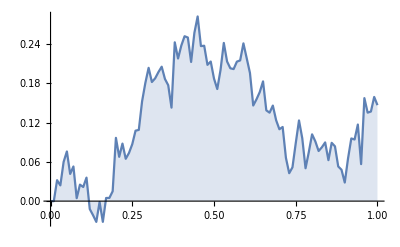

```mathematica
Clear["Global`*"]

(* A Wiener process is also known as Brownian motion,a continuous-time random walk,or integrated white Gaussian noise *)
(* The state at time t follows a NormalDistribution [μ t, σ √t] *)
(* *)

T=1;
sigma=0.3;
r=0.05;
K=10;

data=RandomFunction[WienerProcess[r,sigma],{0,T,0.01}]
ListLinePlot[data,Filling->Axis]
```

```mathematica
Mean[WienerProcess[r,sigma][t]]
```

0.05 t

```mathematica
Variance[WienerProcess[t,sigma][t]]
```

0.09 t

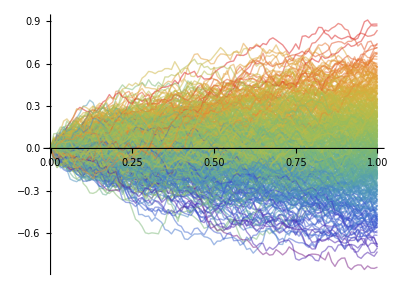

```mathematica
(* simulate 500 Wiener-Walks *)
data500=RandomFunction[WienerProcess[r,sigma],{0,T,0.01},500];
sd=data500["SliceData",1];
cf=ColorData["Rainbow"];
ListLinePlot[data500,ImageSize->400,PlotRange->All,
AspectRatio->3/4,PlotStyle->(cf/@Rescale[sd]),BaseStyle->Directive[Thin,Opacity[0.5]],PlotRangePadding->{{0,.25},{.5,.5}}]
```

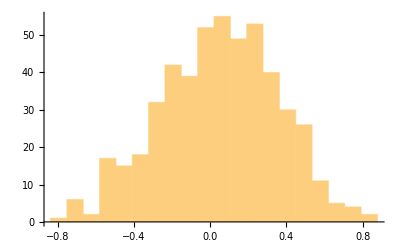

```mathematica
Histogram[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/20]}]
```

```mathematica
DistributionFitTest[sd] (* tests whether data is normally distributed *)
```

0.697585

```mathematica
HH=DistributionFitTest[sd,Automatic,"HypothesisTestData"];
HH["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.445199 | 0.28682
Baringhaus-Henze | 0.463516 | 0.40545
Cramér-von Mises | 0.0606235 | 0.378517
Jarque-Bera ALM | 2.92381 | 0.21411
Kolmogorov-Smirnov | 0.0281787 | 0.444874
Kuiper | 0.0482046 | 0.404811
Mardia Combined | 2.92381 | 0.21411
Mardia Kurtosis | -1.25724 | 0.208667
Mardia Skewness | 1.41656 | 0.233971
Pearson χ^2 | 22.9 | 0.407395
Shapiro-Wilk | 0.996229 | 0.283751
Watson U^2 | 0.0516376 | 0.441303

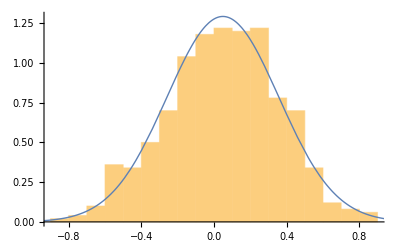

```mathematica
Show[Histogram[sd,Automatic,"ProbabilityDensity"],Plot[PDF[HH["FittedDistribution"],x],{x,-1.5,+1.5},PlotStyle->Thick]]
```

```mathematica
(* Test if the mean of the data is zero *)
LocationTest[sd,Automatic,{"TestDataTable",All}]
```

| Statistic | P-Value
Paired T | 3.54504 | 0.000429512
Paired Z | 3.54504 | 0.000392561
Sign | 286 | 0.00147246
Signed-Rank | 74363. | 0.000282014
T | 3.54504 | 0.000429512
Z | 3.54504 | 0.000392561

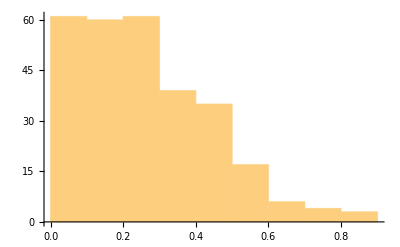

```mathematica
opt=Select[sd,#>0 &];
Histogram[opt]
```

```mathematica
Mean[opt] (* the option is convex, the loss is bounded at 0 *)
Mean[sd] (* mean of the Wiener walk is expected to be 0.05 t *)
```

0.263728

0.048957

```mathematica
FinancialDerivative[{"European","Call"},{"StrikePrice"->0.10,"Expiration"->1},{"InterestRate"->r,"Volatility"->sigma,"CurrentPrice"->0.10}]
FinancialDerivative[{"European","Call"},{"StrikePrice"->1.00,"Expiration"->1},{"InterestRate"->r,"Volatility"->sigma,"CurrentPrice"->1.00}]
FinancialDerivative[{"European","Call"},{"StrikePrice"->10.0,"Expiration"->1},{"InterestRate"->r,"Volatility"->sigma,"CurrentPrice"->10.0}]
```

0.0142313

0.142313

1.42313

```mathematica
dataG500=RandomFunction[GeometricBrownianMotionProcess[r,sigma,10],{0,1,.01},2500]
sdG=dataG500["SliceData",1];
ListLinePlot[dataG500,ImageSize->400,PlotRange->All,
AspectRatio->3/4,PlotStyle->(cf/@Rescale[sd]),BaseStyle->Directive[Thin,Opacity[0.5]],PlotRangePadding->{{0,.25},{.5,.5}}]
```

TemporalData[…]

-Graphics-

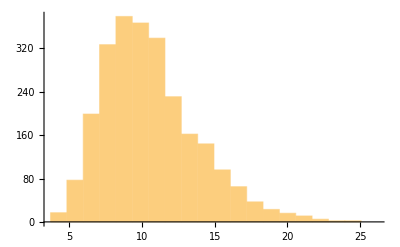

```mathematica
Histogram[sdG,{Range[Min[sdG],Max[sdG],(Max[sdG]-Min[sdG])/20]}]
```

```mathematica
DistributionFitTest[sdG]
```

0

```mathematica
optG=Select[sdG,#>10 &];
Mean[optG]
```

13.0599

```mathematica
Mean[sdG]
```

10.5723

```mathematica
f1=HistogramDistribution[optG];
Moment[f1,1] (* mean *)
```

13.0782

```mathematica
Moment[f1,2] (* variance *)
```

177.946

```mathematica
Quantile[f1,0.95]
```

18.1906

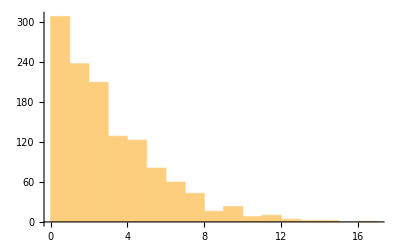

```mathematica
optG1=Select[sdG,#>10 &];
optG1=optG1-10;
Histogram[optG1]
```

```mathematica
h2=HistogramDistribution[sdG];
Moment[h2,1]
```

10.5772

```mathematica
(* finally we want to estimate the value of a call option numerically *)
(* remember: the option value is the expected value of the claim *)
NIntegrate[(x-10)*UnitStep[x-10]*PDF[h2,x],{x,0,20}]
```

1.4216